# Интерполационен полином на Лагранж

## Генериране на данни (съставяне на табличната функция)

```mathematica
xt = Table[3+i*0.1,{i,-5,5}]
```

{2.5,2.6,2.7,2.8,2.9,3.,3.1,3.2,3.3,3.4,3.5}

```mathematica
f[x_]:=13 Sin[x+2]
```

за да сравняваме резултатите визуализираме функцията

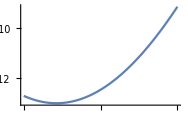

```mathematica
Plot[f[x],{x,2.5,3.5}]
```

```mathematica
yt = f[xt]
```

{-12.7079,-12.918,-12.999,-12.9501,-12.7719,-12.466,-12.0356,-11.4849,-10.8195,-10.0459,-9.17202}

11

{{2.5,-12.7079},{2.6,-12.918},{2.7,-12.999},{2.8,-12.9501},{2.9,-12.7719},{3.,-12.466},{3.1,-12.0356},{3.2,-11.4849},{3.3,-10.8195},{3.4,-10.0459},{3.5,-9.17202}}

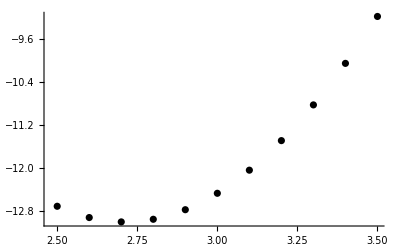

```mathematica
n = Length[xt]
points = Table[{xt[[i]],yt[[i]]},{i,1,n}]
grp = ListPlot[points, PlotStyle->Black]
```

## Интерполация в т. z = 2.97

### Линейна интерполация

```mathematica
L1[x_]:=-12.7719*(x - 3)/(2.9-3)-12.466*(x-2.9)/(3-2.9)
Expand[L1[x]]
```

-21.643+3.059 x

#### Проверка на интерполационните условия

```mathematica
L1[2.9]
L1[3]
```

-12.7719

-12.466

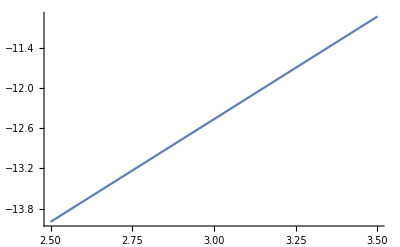

```mathematica
grL1 = Plot[L1[x],{x,2.5,3.5}]
```

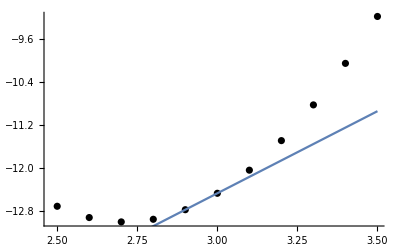

```mathematica
Show[grp,grL1]
```

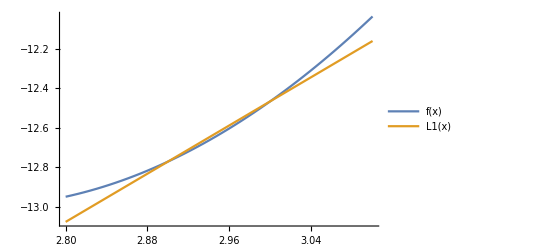

```mathematica
Plot[{f[x],L1[x]},{x,2.8,3.1}, PlotLegends->"Expressions"]
```

#### Пресмятане приближена стойност на функцията в z = 2.97

```mathematica
L1[2.97]
```

-12.5578

#### Oценка на грешката

истинска грешка

```mathematica
Abs[f[2.97]-L1[2.97]]
```

0.0132479

теоретична грешка

намираме M2

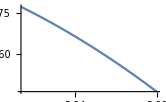

```mathematica
Plot[Abs[f''[x]],{x,2.9,3}]
```

от графиката се вижда, че

```mathematica
M2 = Abs[f''[2.9]]
```

12.7719

```mathematica
R1[x_]:=M2/(2!)*Abs[(x-2.9)(x-3)]
```

```mathematica
R1[2.97]
```

0.0134105

за сравнение истинската грешка е 0.0132479

### Квадратична интерполация

```mathematica
L2[x_]:=-12.7719*((x - 3)(x-3.1))/((2.9-3)(2.9-3.1))-12.466*((x-2.9)(x-3.1))/((3-2.9)(3-3.1))-12.0356*((x-2.9)(x-3.))/((3.1-2.9)(3.1-3.))
Expand[L2[x]]
```

32.5145-33.6685 x+6.225 x^2

#### Проверка на интерполационните условия

```mathematica
L2[2.9]
L2[3]
L2[3.1]
```

-12.7719

-12.466

-12.0356

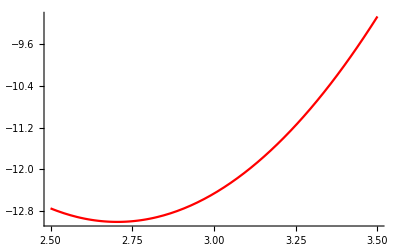

```mathematica
grL2 = Plot[L2[x],{x,2.5,3.5},PlotStyle->Red]
```

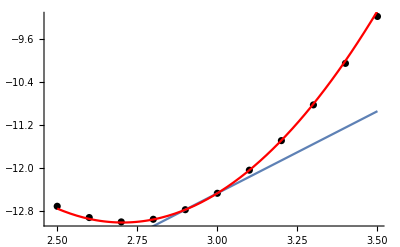

```mathematica
Show[grp,grL1,grL2]
```

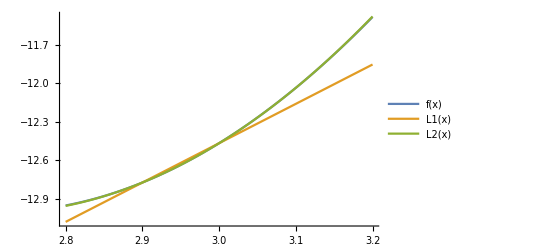

```mathematica
Plot[{f[x],L1[x], L2[x]},{x,2.8,3.2}, PlotLegends->"Expressions"]
```

#### Пресмятане приближена стойност на функцията в z = 2.97

```mathematica
L2[2.97]
```

-12.5708

#### Oценка на грешката

истинска грешка

```mathematica
Abs[f[2.97]-L2[2.97]]
```

0.000175443

теоретична грешка

намираме M3

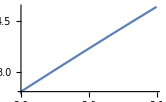

```mathematica
Plot[Abs[f'''[x]],{x,2.9,3.1}]
```

от графиката се вижда, че

```mathematica
M3 = Abs[f'''[3.1]]
```

4.91371

```mathematica
R2[x_]:=M3/(3!)*Abs[(x-2.9)(x-3)(x-3.1)]
```

```mathematica
R2[2.97]
```

0.000223574

за сравнение истинската грешка е 0.000175443

### Кубична интерполация

## Eстраполация в т. z = 3.56 (близка до дадените точки)

## Eстраполация в т. z = 10 (далечна от дадените точки)

```mathematica
L2[10]
```

318.329

```mathematica
R2[10]
```

280.843